```mathematica
<<ACPackages`
```

```mathematica
SetDirectory["D:\\Работа\\Programs\\tormagn\\run\\4"]
```

D:\Работа\Programs\tormagn\run\4

```mathematica
{p,vx,vy,vz,Ax,Ay,Az,nut}=ReadBinarySnapFile["dynamo_2_12820.snp",8];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{10/3,0,0},ProcDistrib->{1,1,2},NumberOfRefs->4];
```

{1,1,2}

{3.08025,12820,64,32,64,100.}

ghost=3

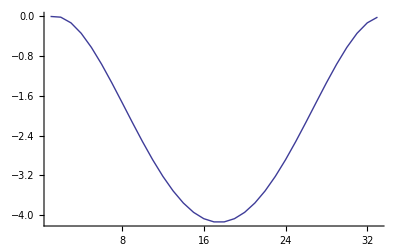

```mathematica
PrintRange[Take[Cut3D[Cut3D[vx,2,10],1,35],{19,51}]]
```

```mathematica
DrawSection[vx,vy,-vz,OnlySection->True]
```

-Graphics-

```mathematica
1/12 ρ^2(1-ρ^2)Sin[ϕ]Cos[ϕ]
```

```mathematica
1/48(ρ^2-1)(1-3 ρ^2+2 ρ^2 Cos[2ϕ])
```

```mathematica
ρ Dϕ Dr=Dr Dϕ ρ
```

```mathematica
Dr[f_]:=D[f,ρ]+(f Cos[ϕ])/(ρ Cos[ϕ]+Subscript[r, c]);
SuperStar[Dr][f_]:=D[f,ρ]-(f Cos[ϕ])/(ρ Cos[ϕ]+Subscript[r, c]);
Dϕ[f_]:=D[f,ϕ]/ρ-(f Sin[ϕ])/(ρ Cos[ϕ]+Subscript[r, c]);
SuperStar[Dϕ][f_]:=D[f,ϕ]/ρ+(f Sin[ϕ])/(ρ Cos[ϕ]+Subscript[r, c]);
Dζ[f_]:=1/(ρ Cos[ϕ]+Subscript[r, c])D[f,ζ];
Λ[f_]:=Dr[Dr[f]]+Subscript[r, c]/(ρ (ρ Cos[ϕ]+Subscript[r, c]))Dr[f]+Dϕ[Dϕ[f]]+Sin[ϕ]/(ρ Cos[ϕ]+Subscript[r, c])Dϕ[f]
Δ[f_]:=Dr[Dr[f]]+Subscript[r, c]/(ρ (ρ Cos[ϕ]+Subscript[r, c]))Dr[f]+Dϕ[Dϕ[f]]+Sin[ϕ]/(ρ Cos[ϕ]+Subscript[r, c])Dϕ[f]+D[f,ζ,ζ]/(ρ Cos[ϕ]+Subscript[r, c])^2+f/(ρ Cos[ϕ]+Subscript[r, c])^2
Subscript[Δ, cyl][f_]:=D[f,{θ⟦1⟧,2}]+1/θ⟦1⟧D[f,θ⟦1⟧]+1/θ⟦1⟧^2 D[f,{θ⟦3⟧,2}]
M=κ ρ Cos[ϕ]+1;
```

```mathematica
DSolve[{D[r[z,t],t]==-D[α f[z,t],z]+D[r[z,t],z,z],D[f[z,t],t]==D r[z,t],f[1,0]==r[1,0]==0,D[f[0,t],z]==D[r[0,t],z]==0,r[0,t]==z[0,t]==0},{f,r},{z,t}]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument SuperscriptBox[SuperscriptBox[f[1, 0] == r[1, 0] == 0Truer[0, t] == z[0, t] == 0.

DSolve[{r^(0,1)[z,t]==-α f^(1,0)[z,t]+r^(2,0)[z,t],f^(0,1)[z,t]==D r[z,t],f[1,0]==r[1,0]==0,True,r[0,t]==z[0,t]==0},{f,r},{z,t}]